```mathematica
f11[m_]:=1-(3 π^2)/8 m^2+(π^2-(5 π^4)/128)m^4+(π^2/9-(11 π^4)/72+(119 π^6)/15360)m^6+5.0779 m^8-2.88312 m^10-0.0925 m^12+2.996 m^14-4.059 m^16+1.63 m^18+4.1 m^20
```

```mathematica
f12[m_]:=(-3π)/2 m+((10π)/3+π^3/16)m^3+(-2π-(133 π^3)/180+(59 π^5)/1280)m^5+12.313906 m^7-7.32433 m^9+1.5793 m^11+4.0216 m^13-6.915 m^15+4.21 m^17+4.56 m^19
```

```mathematica
f21[m_]:=π/2 m-((4π)/3+π^3/48)m^3+((-2π)/3+(13 π^3)/30-(59 π^5)/3840)m^5-6.176023 m^7+4.44112 m^9-1.534 m^11-2.07 m^13+4.684 m^15-3.95 m^17-1.32 m^19
```

```mathematica
f22[m_]:=1-(4+(3 π^2)/8)m^2+(8/3+(29 π^2)/18-(5 π^4)/128)m^4+(-32/15-(4 π^2)/9-(1159 π^4)/7200+(119 π^6)/15360)m^6+10.58254 m^8-4.78511 m^10-1.8804 m^12+7.28 m^14-7.591 m^16+0.25 m^18+12.5 m^20
```

```mathematica
err[x_,y_,m_]:=(f11[m]x+f12[m]y)^2+(f21[m]x+f22[m]y)^2
```

```mathematica
merr[x_,y_?NumericQ]:=First[NMaximize[{err[x,y,m],m<1/2&&m>-1/2},m]]
```

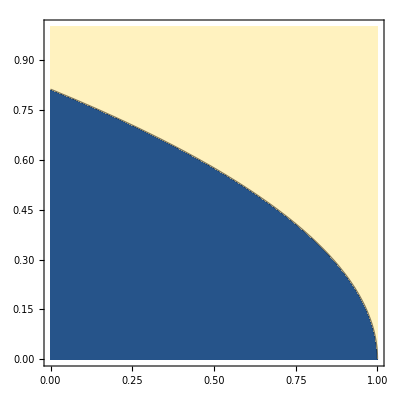

```mathematica
ContourPlot[merr[x,y],{x,0,1},{y,0,1},Contours->{1}]
```

```mathematica
angle[x_,y_]:=m/.Last[NMaximize[{err[x,y,m],m<1/2&&m>-1/2},m]]
```

```mathematica
k2[k1_]:=y/.FindRoot[merr[k1,y]==1,{y,0.8*(1-k1)}]
```

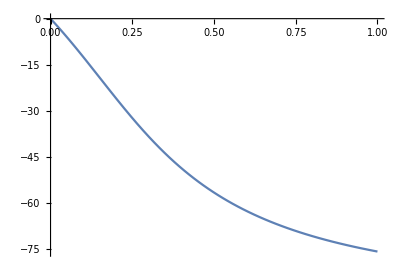

```mathematica
ParametricPlot[{k2[k1]/(k1+k2[k1]),180*angle[k1,k2[k1]]},{k1,0,1},AspectRatio->.7]
```